```mathematica
f1[x1_,x2_]=x1*r1*((x1-c1)/(x1+c1)*(1-x1/k1))-a*x1*x2
f2[x1_,x2_]=x2*r2*((x2-c2)/(x2+c2)*(1-x2/k2))-a*x1*x2
```

(r1 x1 (-c1+x1) (1-x1/k1))/(c1+x1)-a x1 x2

-a x1 x2+(r2 x2 (-c2+x2) (1-x2/k2))/(c2+x2)

```mathematica
r1=0.05;
r2=0.08;
k1=150000;
k2=400000;
a=10^-8;
c1=3000;
c2=15000;
```

```mathematica
Solve[{f1[x1,x2]==0,f2[x1,x2]==0, x1≠ 0, x2≠0},{x1,x2}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→3018.44+0. ⅈ,x2→15011.8+0. ⅈ},{x1→3535.18+0. ⅈ,x2→399809.+0. ⅈ},{x1→137698.+0. ⅈ,x2→392568.+0. ⅈ},{x1→149513.+0. ⅈ,x2→15595.+0. ⅈ}}

```mathematica
Solve[{f1[x1,x2]/x1==0,f2[x1,x2]/x2==0, x1≠ 0, x2≠0},{x1,x2}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→3018.44+0. ⅈ,x2→15011.8+0. ⅈ},{x1→3535.18+0. ⅈ,x2→399809.+0. ⅈ},{x1→137698.+0. ⅈ,x2→392568.+0. ⅈ},{x1→149513.+0. ⅈ,x2→15595.+0. ⅈ}}

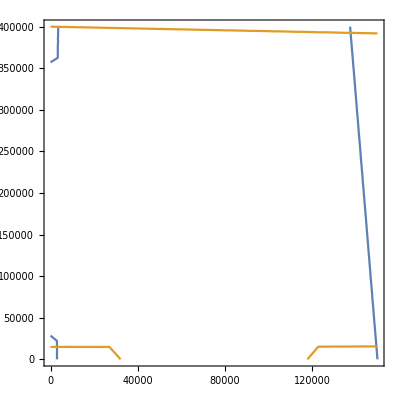

```mathematica
ContourPlot[{f1[x1,x2]==0,f2[x1,x2]==0},{x1,0,150000},{x2,0,400000}]
```

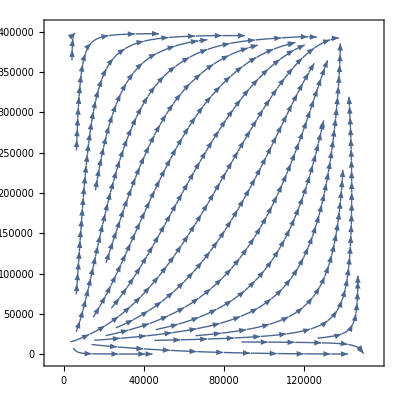

```mathematica
StreamPlot[{f1[x1,x2],f2[x1,x2]},{x1,0,150000},{x2,0,400000}]
```

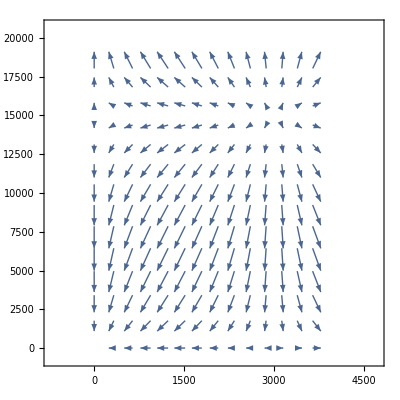

```mathematica
VectorPlot[{f1[x1,x2],f2[x1,x2]},{x1,0,4000},{x2,0,20000}]
(*Near (x1,x2)=(3000,15000)*)
```

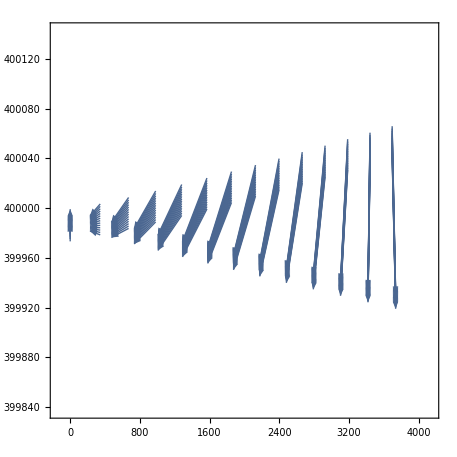

```mathematica
VectorPlot[{f1[x1,x2],f2[x1,x2]},{x1,0,4000},{x2,399980,400000}]
(*Near (x1,x2)=(3000,400000)*)
```

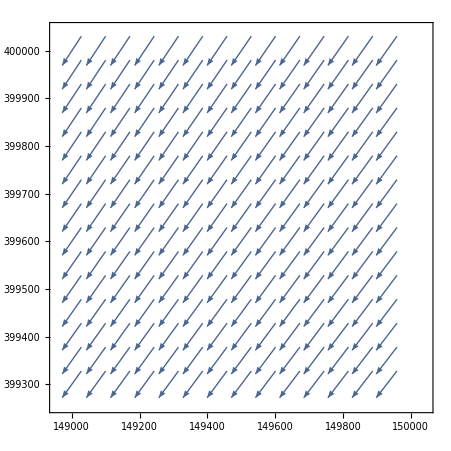

```mathematica
VectorPlot[{f1[x1,x2],f2[x1,x2]},{x1,149000,150000},{x2,399300,400000}]
(*Near (x1,x2)=(3000,400000)*)
```

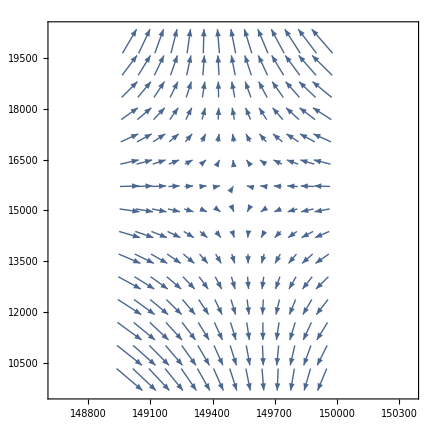

```mathematica
VectorPlot[{f1[x1,x2],f2[x1,x2]},{x1,149000,150000},{x2,10000,20000}]
(*Near (x1,x2)=(3000,400000)*)
```

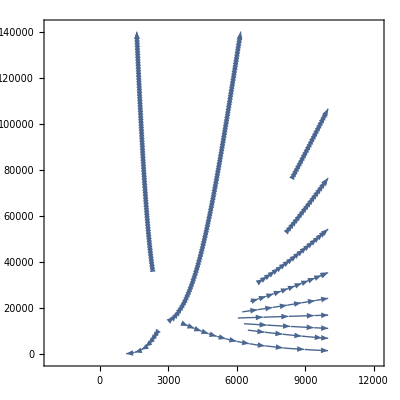

```mathematica
StreamPlot[{f1[x1,x2],f2[x1,x2]},{x1,0,10000},{x2,0,140000}]
```

```mathematica
c1=10000
```

10000

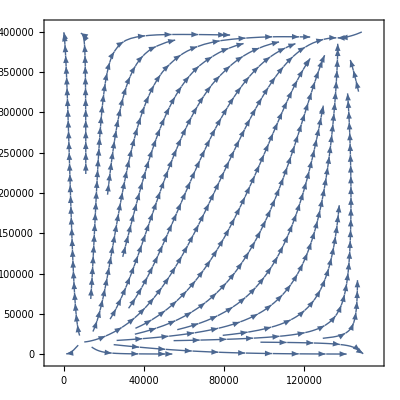

```mathematica
StreamPlot[{f1[x1,x2],f2[x1,x2]},{x1,0,150000},{x2,0,400000}]
```

```mathematica
df1dx1[x1_,x2_]=D[f1[x1,x2],x1]
df1dx2[x1_,x2_]=D[f1[x1,x2],x2]
df2dx1[x1_,x2_]=D[f2[x1,x2],x1]
df2dx2[x1_,x2_]=D[f2[x1,x2],x2]
```

-(0.05 (1-x1/150000) (-3000+x1) x1)/(3000+x1)^2+(0.05 (1-x1/150000) (-3000+x1))/(3000+x1)+(0.05 (1-x1/150000) x1)/(3000+x1)-(3.33333×10^-7 (-3000+x1) x1)/(3000+x1)-x2/100000000

-x1/100000000

-x2/100000000

-x1/100000000-(0.08 (1-x2/400000) (-15000+x2) x2)/(15000+x2)^2+(0.08 (1-x2/400000) (-15000+x2))/(15000+x2)+(0.08 (1-x2/400000) x2)/(15000+x2)-(2.×10^-7 (-15000+x2) x2)/(15000+x2)

```mathematica
jacobian[x1_,x2_]={{df1dx1[x1,x2],df1dx2[x1,x2]},{df2dx1[x1,x2],df2dx2[x1,x2]}}
```

{{-(0.05 (1-x1/150000) (-3000+x1) x1)/(3000+x1)^2+(0.05 (1-x1/150000) (-3000+x1))/(3000+x1)+(0.05 (1-x1/150000) x1)/(3000+x1)-(3.33333×10^-7 (-3000+x1) x1)/(3000+x1)-x2/100000000,-x1/100000000},{-x2/100000000,-x1/100000000-(0.08 (1-x2/400000) (-15000+x2) x2)/(15000+x2)^2+(0.08 (1-x2/400000) (-15000+x2))/(15000+x2)+(0.08 (1-x2/400000) x2)/(15000+x2)-(2.×10^-7 (-15000+x2) x2)/(15000+x2)}}

```mathematica
MatrixForm[jacobian[0,0]]
MatrixForm[jacobian[150000,0]]
MatrixForm[jacobian[0,400000]]
MatrixForm[jacobian[137698,392568]]
MatrixForm[jacobian[3000,0]]
MatrixForm[jacobian[0,15000]]
MatrixForm[jacobian[3018.44,15011.8]]
MatrixForm[jacobian[3535.18,399809]]
MatrixForm[jacobian[149513,15595]]
```

(-0.05 | 0
0 | -0.08)

(-0.0480392 | -3/2000
0 | -0.0815)

(-0.054 | 0
-1/250 | -0.0742169)

(-0.0437707 | -68849/50000000
-49071/12500000 | -0.072629)

(0.0245 | -3/100000
0 | -0.08003)

(-0.05015 | 0
-3/20000 | 0.0385)

(0.0244936 | -0.0000301844
-0.000150118 | 0.0384977)

(0.0241506 | -0.0000353518
-399809/100000000 | -0.074176)

(-0.0478707 | -149513/100000000
-3119/20000000 | 0.0383653)

```mathematica
Eigensystem[jacobian[0,0]]
Eigensystem[jacobian[150000,0]]
Eigensystem[jacobian[0,400000]]
Eigensystem[jacobian[137698,392568]]
Eigensystem[jacobian[3000,0]]
Eigensystem[jacobian[0,15000]]
Eigensystem[jacobian[3018.44,15011.8]]
Eigensystem[jacobian[3535.18,399809]]
Eigensystem[jacobian[149513,15595]]
```

{{-0.08,-0.05},{{0.,1.},{-1.,0.}}}

{{-0.0815,-0.0480392},{{0.0447836,0.998997},{1.,0.}}}

{{-0.0742169,-0.054},{{0.,1.},{0.980983,-0.194092}}}

{{-0.0728151,-0.0435846},{{0.0473563,0.998878},{0.990989,-0.133943}}}

{{-0.08003,0.0245},{{0.000286999,1.},{1.,0.}}}

{{-0.05015,0.0385},{{0.999999,0.00169204},{0.,1.}}}

{{0.038498,0.0244933},{{0.00215534,-0.999998},{-0.999943,-0.0107187}}}

{{-0.0741775,0.024152},{{0.000359529,1.},{0.999174,-0.0406271}}}

{{-0.0478735,0.038368},{{-0.999998,-0.00180835},{0.0173345,-0.99985}}}